```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
Npoints=100;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]
M=32;
M2=3;
A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*2*n+I*ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]
A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
κ=1;
η=0.1;
```

/home/zack/oscillators/anharmonic

## Direct simulations

```mathematica
filebase="data/anharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Dimensions[dat]
norms=Total/@Abs[dat[[All,1;;32]]]^2/M;
max=Max[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
min=Min[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
n0=1001;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat[[n0/dt]]]^2]&/@dat]]],2][[-1,1]];
power=Abs[Fourier[dat[[n0/dt;;n2,1]]]];
freqs=Range[Length[dat[[n0/dt;;n2,1]]]]/(Length[dat[[n0/dt+1;;n2,1]]]*dt);
n0=500;
Grid[{{rasterizeBackground[ListPlot[Log[norms],Joined->True,ImageSize->300,ImageSize->300,AspectRatio->1,PlotRange->All]],rasterizeBackground[ListPlot[{dat[[-500;;-1,1]],Cos[2*Pi*dt*Range[500]]},PlotRange->All,Joined->True,ImageSize->300,AspectRatio->1]],rasterizeBackground[ListDensityPlot[Mod[dat[[1;;-1;;2*Round[1/dt],1;;M]]+Pi,2*Pi]-Pi,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0,ImageSize->300,AspectRatio->1]],rasterizeBackground[ListLogPlot[{Transpose[{freqs,power}]},PlotRange->{{0,3},All},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-5,2,2}],Table[{10^i,""},{i,-5,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,3,0.5}],Table[{i,""},{i,0,3,0.5}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]],rasterizeBackground[ListPlot[{Transpose[{dt*Range[n0],Mod[dat[[-n0;;-1,1]]+Pi,2*Pi]-Pi}],Transpose[{dt*Range[n0],Mod[dat[[-n0;;-1,2]]+Pi,2*Pi]-Pi}]},PlotRange->All,Joined->True,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->350,AspectRatio->1]]}}]
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

{100000,64}

0.865348

-1.07434

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Schematic and dispersion

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

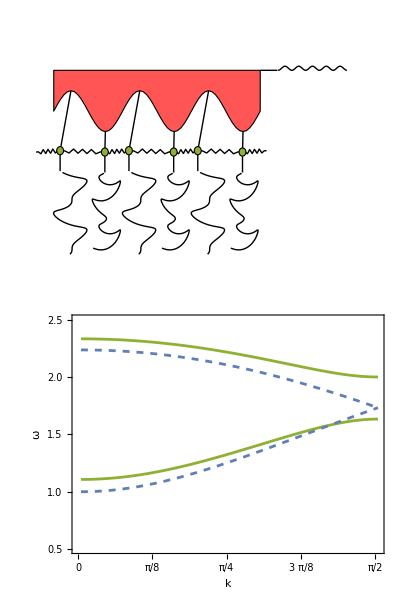

fig1.pdf

```mathematica
filebase="data/anharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
dx=1;
M=6;
n=Length[dat];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->500,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}];
p1=Show[ListPlot[Transpose[Table[Re[ω/.dispersion/.Δ->0.5],{q,0,Pi,Pi/100}]],Joined->True,PlotRange->{0.5,2.5},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{25,DisplayForm[RowBox[{"π","/",8}]]},{50,DisplayForm[RowBox[{"π","/",4}]]},{75,DisplayForm[RowBox[{3"π","/",8}]]},{100,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,100,25}]}},Axes->False,Frame->True,FrameLabel->{k,ω},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImageSize->350,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],AspectRatio->1/2],
ListPlot[Transpose[Table[Re[ω/.dispersion/.Δ->0.0],{q,0,Pi,Pi/100}]],Joined->True,PlotRange->{0,3},Axes->False,Frame->True,FrameLabel->{k,ω},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImageSize->350,PlotStyle->Directive[Dashed,AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],AspectRatio->1/3]];
p=Grid[{{p0},{p1}}]
Export["fig1.pdf",p]
```

## Floquet exponents

{-4.46689+0.03125 ⅈ,4.46689+0.03125 ⅈ,3.71839+0.03125 ⅈ,-3.71839+0.03125 ⅈ,-3.43331+0.03125 ⅈ,3.43331+0.03125 ⅈ,-2.61283+0.03125 ⅈ,2.61283+0.03125 ⅈ,2.42222+0.101842 ⅈ,-2.42222+0.101842 ⅈ,2.42222-0.0393418 ⅈ,-2.42222-0.0393418 ⅈ,-1.60621+0.0760227 ⅈ,1.60621+0.0760227 ⅈ,1.60621-0.0135227 ⅈ,-1.60621-0.0135227 ⅈ,-1.3984+0.0757859 ⅈ,1.3984+0.0757859 ⅈ,1.3984-0.0132859 ⅈ,-1.3984-0.0132859 ⅈ,-0.601987+0.0743008 ⅈ,0.601987+0.0743008 ⅈ,-0.601987-0.0118008 ⅈ,0.601987-0.0118008 ⅈ,0.398029+0.0742969 ⅈ,-0.398029+0.0742969 ⅈ,0.398029-0.0117969 ⅈ,-0.398029-0.0117969 ⅈ}

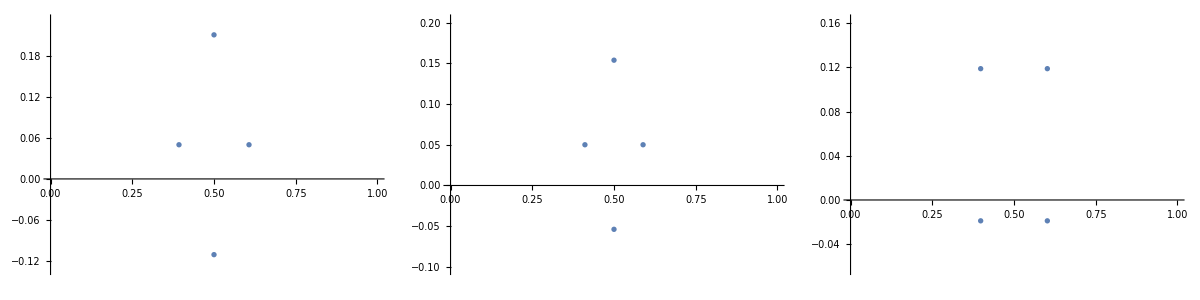

{2.82868×10^-15-2.07993×10^-15 ⅈ,-1.96189×10^-14+3.2036×10^-15 ⅈ,1.99493×10^-15+1.81799×10^-15 ⅈ,-1.21084×10^-15+1.68129×10^-14 ⅈ,2.77556×10^-16+2.72005×10^-15 ⅈ,4.31252×10^-15+6.93889×10^-15 ⅈ,1.07553×10^-15+1.24293×10^-15 ⅈ,9.4022×10^-16-4.79651×10^-16 ⅈ,-6.66134×10^-16-1.4988×10^-15 ⅈ,-1.77636×10^-15+1.66533×10^-15 ⅈ,-3.83027×10^-15-4.996×10^-16 ⅈ,1.24553×10^-15+8.60423×10^-16 ⅈ,6.73767×10^-15+1.60982×10^-15 ⅈ,9.33455×10^-15+1.87524×10^-15 ⅈ}

{{0.601987,0.118881},{0.601987,-0.0188813},{0.398029,0.118875},{0.398029,-0.0188751}}

```mathematica
ω=1.6;
κ=1;
Δ=0.5;
q=0;
a=0.4;
{evals,evecs}=Eigensystem[{A[a,ω,Δ,q],B[a,ω,Δ,q]}];
evals
Grid[{{ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,0,q],B[a,ω,0,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ/2,q],B[a,ω,Δ/2,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],PlotRange->{{0,1},All},ImageSize->300]}}]
val=evals[[-1]];
vec=evecs[[-1,1;;2*(2*M2+1)]];
val^2*A1[a,ω,Δ,q].vec+val*A2[a,ω,Δ,q].vec+A3[a,ω,Δ,q].vec
Cases[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;u[[1]]>0&&u[[1]]<1]
```

### Individual parameters

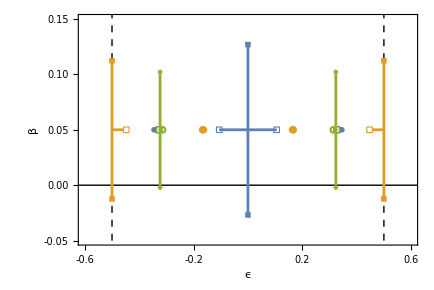

```mathematica
Clear[ω]
ωd=1.0;
Δ=0.5;
amin=0.01;
amax=0.8;
q=0;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]],PlotMarkers->{Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[1]]], White, Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}}]];
ωd=2.0;
amin=0.01;
amax=0.12;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[5;;6]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
ωd=3.4;
amin=0.0;
amax=0.05;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p3=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p1=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->435,ImagePadding->{{75,15},{75,15}},FrameTicks->{{Table[{i,PaddedForm[N[i],{3,2}]},{i,-0.05,0.15,0.05}],Table[{i,""},{i,-0.05,0.15,0.05}]},{Table[{i,PaddedForm[N[i],{2,1}]},{i,-6/10,6/10,2/10}],Table[{i,""},{i,-6/10,6/10,2/10}]}}]
```

```mathematica
ωd=3.4;
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ωd,0,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ωd,Δ,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ωd,0,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ωd,Δ,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
```

{1.97117,Null}

{2.0806,Null}

{2.14176,Null}

{2.21178,Null}

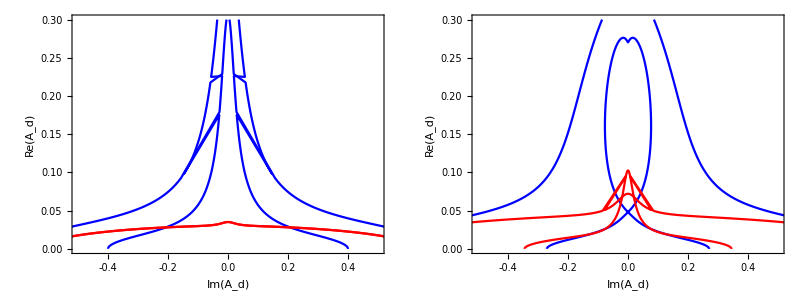
-Graphics-
-Graphics-

fig4.pdf

```mathematica
p2=Grid[{{Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[Blue]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[Red]]],Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[Blue]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[Red]]]}}];
p=Grid[{{p1},{p2}}]
Export["fig4.pdf",p]
```

### Large sweep

```mathematica
M=100;
Δ=0.5;
κ=1;
ωmin=1.0;
ωmax=2.0;
amin=0;
amax=1.0;
num=100;

AbsoluteTiming[Monitor[vals=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
min=0;
max=0.5;
Clear[ω]
cf1[x_]:=If[x<-0.01,White,If[x≤min,Lighter[Cyan],If[x>max,Lighter[Orange],Blend[{Lighter[Cyan],Lighter[Orange]},(x-min)/(max-min)]]]];
cf2[x_]:=Lighter[ColorData["Rainbow"][0.25+0.5*(x-0)/(Pi-0)]];
Grid[{{Legended[rasterizeBackground[Show[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf1,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]],Placed[MatrixPlot[Table[cf1[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],Above]],Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,All,{0,2*Pi}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf2),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf2[Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",8}]]},{50,DisplayForm[RowBox[{π,"/",4}]]},{75,DisplayForm[RowBox[{3π,"/",8}]]},{100,DisplayForm[RowBox[{π,"/",2}]]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->k,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],Above]]}}]
```

{973.927,Null}

-Graphics- | -Graphics-

```mathematica
Export["vals.dat", vals]
```

vals.dat

```mathematica
M=100;
Δ=0.5;
ωmin=1.0;
ωmax=2.0;
amin=0;
amax=1.0;
num=250;AbsoluteTiming[Monitor[vals1=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals1.dat",vals1]
```

```mathematica
M=100;
Δ=0.5;
ωmin=3.0;
ωmax=4.0;
amin=0;
amax=0.1;
num=250;
AbsoluteTiming[Monitor[vals2=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals2.dat",vals2]
```

{5203.84,Null}

```mathematica
M=100;
Δ=0.5;
ωmin=1.0;
ωmax=3.0;
amin=0;
amax=0.25;
num=250;
AbsoluteTiming[Monitor[vals3=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals3.dat",vals3]
```

{2267.16,Null}

```mathematica
M=32;
Δ=0.5;
ωmin=4.0;
ωmax=10.0;
amin=0;
amax=1.0;
num=50;AbsoluteTiming[Monitor[vals4=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals4.dat",vals4]
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

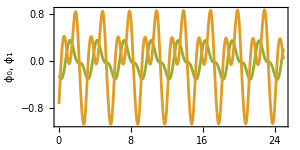
-Graphics-
-Graphics-

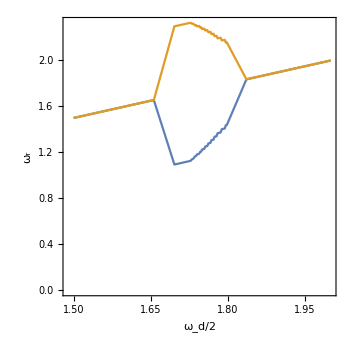
-Graphics- | -Graphics-
-Graphics-

fig2.pdf

```mathematica
filebase="data/anharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat1=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
filebase="data/noisy";
dat2=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];

Clear[t];
p1=ListPlot[{Transpose[{dt*Range[500],dat1[[-500;;-1,1]]}],Transpose[{dt*Range[500],dat1[[-500;;-1,2]]}]},PlotRange->All,Joined->True,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2];

n0=1000;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat1[[n0/dt]]]^2]&/@dat1]]],2][[-1,1]];
power1=Abs[Fourier[dat1[[n0/dt;;n2,1]]]];
freqs1=Range[Length[dat1[[n0/dt;;n2,1]]]]/(Length[dat1[[n0/dt+1;;n2,1]]]*dt);
power2=Abs[Fourier[dat2[[n0/dt;;n2,1]]]];
freqs2=Range[Length[dat2[[n0/dt;;n2,1]]]]/(Length[dat2[[n0/dt+1;;n2,1]]]*dt);
p2=Legended[rasterizeBackground[ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}]},PlotRange->{{0,1},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2]],Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]]},{DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.,{2,1}]}]],DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.1,{2,1}]}]]},LabelStyle->Directive[13]],{0.82,0.7}]];
p0=Grid[{{p1},{p2}}]
p1=ListPlot[{{#[[1]]/2,#[[1]]*#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05],{#[[1]]/2,#[[1]]*(1-#[[4]])}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05]},Joined->True,InterpolationOrder->1,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[ω,r]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImagePadding->{{65,15},{65,10}},ImageSize->350];
p=Grid[{{p1,p0}}]
Export["fig2.pdf",p]
```

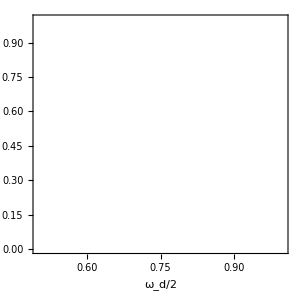
-Graphics- | -Graphics-

fig3.pdf

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
min=0.3;
max=0.5;
c1=Lighter[Cyan];
c2=Lighter[Red];
cf[x_]:=If[x<-0.01,White,If[x≤min,c1,If[x>max,c2,Blend[{c1,c2},(x-min)/(max-min)]]]];
Clear[ω]
p1=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]}]];

p2=rasterizeBackground[Show[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]];
p=Legended[Grid[{{p2,p1}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
Export["fig3.pdf",p]
```

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
min=0.3;
max=0.5;
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
Clear[ω]
p1=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]}]];

p2=rasterizeBackground[Show[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]];
p=Legended[Grid[{{p2,p1}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
Export["fig3.pdf",p]
```

-Graphics- | -Graphics-

fig3.pdf

## Animations

#### harmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/harmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals.dat"];
amin=0.01;
evals1=SortBy[Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
evals2=SortBy[Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
count=0;
n0=Max[1,Length[dat]-499];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
Clear[ω]
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
Export["colobar.pdf",p2]
```

{32,1.,0.8,0.05,0.1,0.,0.5,5000.,1,1}

colobar.pdf

{3.85368,Null}

{19.6501,Null}

{30.3192,Null}

{39.9795,Null}

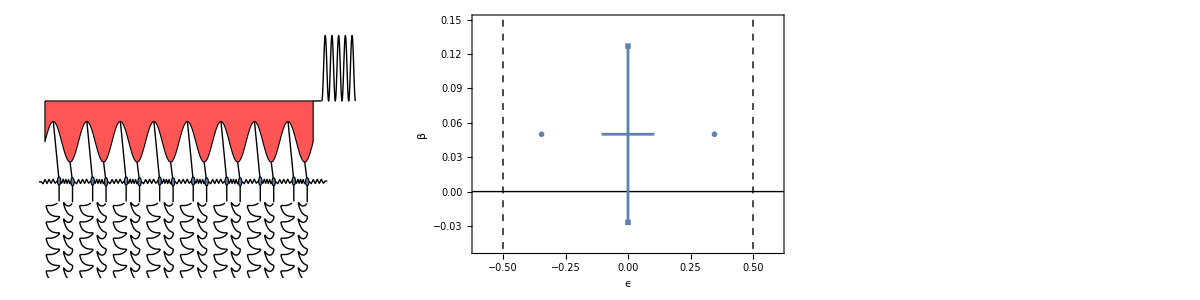

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=SortBy[Cases[Eigenvalues[{A[a,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count2=Round[(n-n0)/20];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count2]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=SortBy[Cases[Eigenvalues[{A[a,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[{1,4}]],{Re[#],ωd*Im[#]}&/@evals[[{2,3}]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.08]],PlotMarkers->{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=SortBy[Cases[Eigenvalues[{A[a,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{13.5568,Null}

{3.73767,Null}

{12.1121,Null}

{67.8754,Null}

#### subharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/subharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals.dat"];
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
count=0;
n0=Max[1,Length[dat]-499];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,2.,0.12,0.05,0.1,0.,0.5,5000.,1,1}

{3.84589,Null}

{15.2633,Null}

{8.24749,Null}

{31.0876,Null}

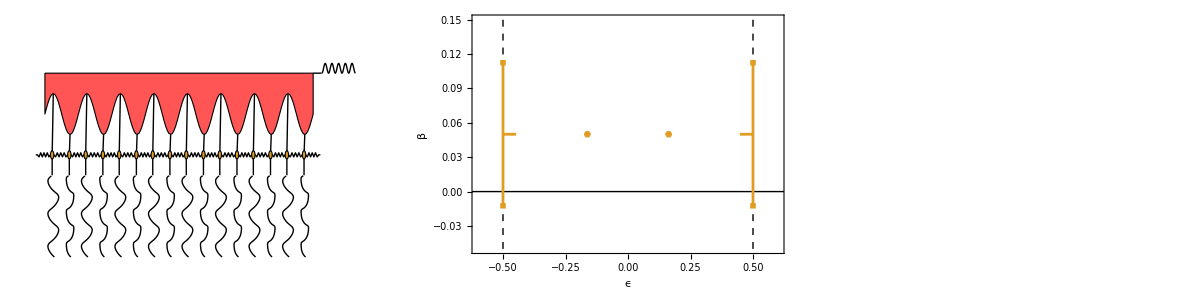

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p1=Show[ListPlot[If[Length[evals]<6,{{Re[#],ωd*Im[#]}&/@evals[[{3,4}]],{Re[#],ωd*Im[#]}&/@evals[[{1,2}]]},{{Re[#],ωd*Im[#]}&/@evals[[5;;6]],{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]}],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.08]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{13.5293,Null}

{4.32614,Null}

{12.1001,Null}

{66.6763,Null}

#### anharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/anharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals2.dat"];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,0.1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

{3.79905,Null}

{16.7237,Null}

{8.17825,Null}

{29.2488,Null}

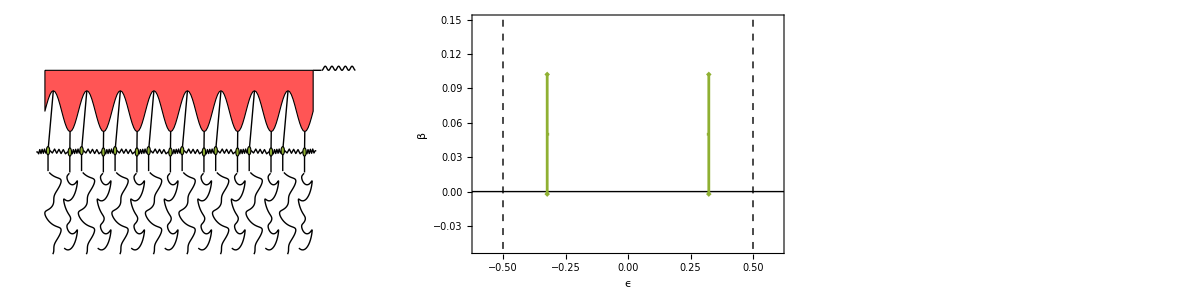

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{13.392,Null}

{4.1612,Null}

{12.186,Null}

{66.2335,Null}

#### anharmonic2

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/anharmonic2";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals.dat"];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,1.6,0.4,0.05,0.1,0.,0.5,5000.,1,1}

{3.8127,Null}

{16.6009,Null}

{8.15524,Null}

{56.7042,Null}

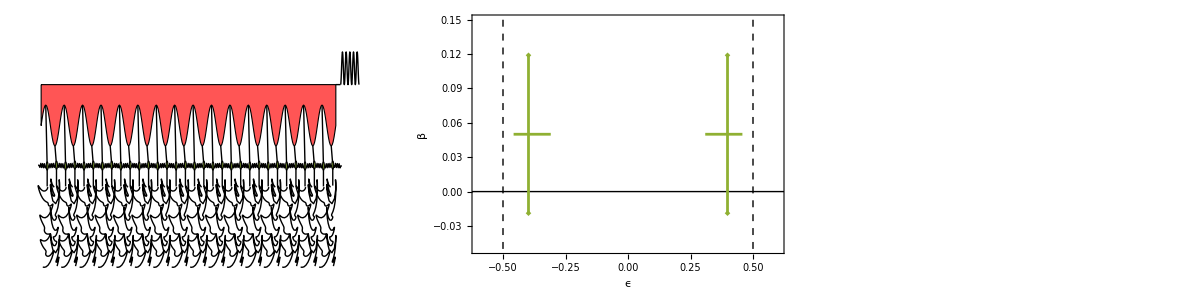

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{13.5509,Null}

{4.1224,Null}

{11.9576,Null}

{111.832,Null}

#### subharmonic2

{32,2.,0.15,0.05,0.1,0.,0.5,1000.,1,1}

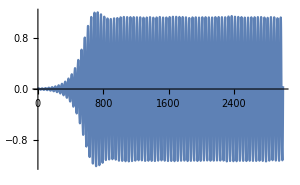

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/subharmonic2";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
ω1=ωd/2;
ω2=ωd;
n0=101;
M=16;
frames=3000;
response=dat[[n0;;n0+frames,2]];
ListPlot[response,ImageSize->300,Joined->True,Axes->{False,True},PlotRange->All]
```

{52.4982,Null}

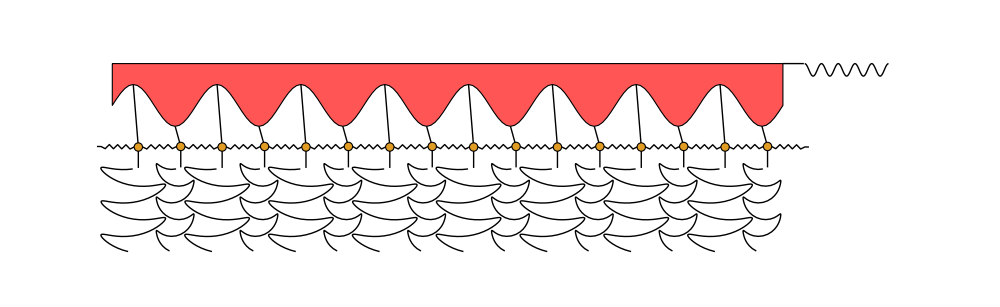

```mathematica
Monitor[AbsoluteTiming[plots=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
a[m_]:=Piecewise[{{amin,(m-n0)<frames/5},{amin+(amax-amin)/(frames/5)*(m-n0-frames/5),(m-n0)<frames*2/5},{amax, True}}];
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=Piecewise[{{ω1*t[m-n0],(m-n0)≤ frames*2/5},{ω1*t[m-n0]+1/2*(ω2-ω1)*(t[m-n0]-t[2*frames/5])^2/(t[3*frames/5]-t[2*frames/5]),(m-n0)≤ 3*frames/5},{ω2*t[m-n0]-(ω2-ω1)*(t[3*frames/5]+t[2*frames/5])/2, True}}];
thetas=If[(n-n0)<3*frames/5,ConstantArray[0,M],dat[[n0+n-3*frames/5,1;;M]]];
thetas2=Table[If[(m-n0)<3*frames/5,ConstantArray[0,M],dat[[n0+m-3*frames/5,1;;M]]],{m,n-100,n}];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p=Graphics[{Black, 
Table[Line[{z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas[[n]]],Cos[thetas[[n]]]},{0,-1/2}+z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas[[n]]],Cos[thetas[[n]]]}}],{n,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas2[[101-m,n]]],Cos[thetas2[[101-m,n]]]}-{0,0.02*m},{m,1,100}]],{n,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,n0+frames}];],{PaddedForm[N[(n-n0)/frames],{3,3}],p}]
plots[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots[[n]]], {n,1,Length[plots]}]]
```

{83.2426,Null}